# Stochastic processes

We examine a few stochastic processes, and practice with random variables.

```mathematica
ClearAll["Global`*"]
```

Generate a pseudorandom real number between 0 and 2π.

```mathematica
RandomReal[{0,2Pi}]
```

2.82534

#### Random walk (first order)

We create a random walk function which takes in initial conditions, number of time-steps, and distance traveled per time-step.

```mathematica
RandomWalkFirstOrder[init_,steps_,distance_,OptionsPattern[{plot->True}]]:=Module[{},
solutions={init};
direction[]:=Module[{},t=RandomReal[{0,2Pi}];{{Cos[t]},{Sin[t]}}];

n=2;

minX=init[[1]];
maxX=init[[1]];
minY=init[[2]];
maxY=init[[2]];

While[n≤steps,
curSol=solutions[[n-1]];
newSol=curSol+distance direction[];
minX=Min[minX,newSol[[1]]];
maxX=Max[maxX,newSol[[1]]];
minY=Min[minY,newSol[[2]]];
maxY=Max[maxY,newSol[[2]]];
solutions=Append[solutions,newSol];
n+=1];

absMin=Min[minX,minY];
absMax=Max[maxX,maxY];

solutions=Level[solutions[[#]],{-1}]&/@Range[steps];
If[OptionValue[plot],
ListPlot[
solutions,Joined->True,AspectRatio->1,
PlotRange->{{absMin,absMax},{absMin,absMax}}
],
solutions]
]
```

Running RandomWalkFirstOrder.

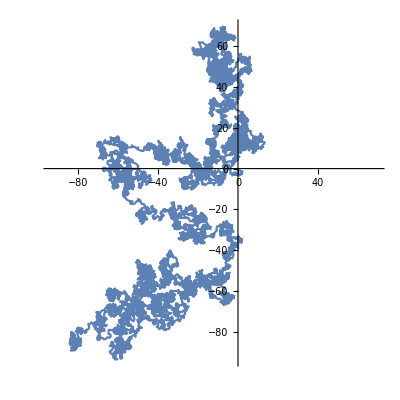

```mathematica
RandomWalkFirstOrder[{{0},{0}},10000,1]
```